```mathematica
FourierTransform[Sin[y]/2,y,k,FourierParameters->{1,1}]
```

1/2 ⅈ π DiracDelta[-1+k]-1/2 ⅈ π DiracDelta[1+k]

```mathematica
FourierTransform[Exp[I j x],x,s,FourierParameters->{1,1}]
```

2 π DiracDelta[j+s]

```mathematica
α[j_]:=If[j≥0,a[j],Conjugate[a[-j]]]
```

```mathematica
Expand[(Sum[α[j]Exp[I j y],{j,-1,1}])^2]
```

a[0]^2+2 ⅇ^(ⅈ y) a[0] a[1]+ⅇ^(2 ⅈ y) a[1]^2+2 ⅇ^(-ⅈ y) a[0] Conjugate[a[1]]+2 a[1] Conjugate[a[1]]+ⅇ^(-2 ⅈ y) Conjugate[a[1]]^2

```mathematica
Sum[Sum[If[(Abs[j]≥2)||(Abs[k-j]≥2) ,0,α[j]α[k-j]],{j,-1,1}]Exp[I k y],{k,-2,2}]
```

a[0]^2+2 ⅇ^(ⅈ y) a[0] a[1]+ⅇ^(2 ⅈ y) a[1]^2+2 ⅇ^(-ⅈ y) a[0] Conjugate[a[1]]+2 a[1] Conjugate[a[1]]+ⅇ^(-2 ⅈ y) Conjugate[a[1]]^2

```mathematica
Collect[FourierTransform[Expand[(Sum[α[j]Exp[I j y],{j,-1,1}])^2],y,k,FourierParameters->{1,1}] ,{DiracDelta[k],DiracDelta[i_+k]}]
```

2 π Conjugate[a[1]]^2 DiracDelta[-2+k]+4 π a[0] Conjugate[a[1]] DiracDelta[-1+k]+(2 π a[0]^2+4 π a[1] Conjugate[a[1]]) DiracDelta[k]+4 π a[0] a[1] DiracDelta[1+k]+2 π a[1]^2 DiracDelta[2+k]

```mathematica
Expand[(Sum[α[j]Exp[I j y],{j,-5,5}])^2]
```

a[0]^2+2 ⅇ^(ⅈ y) a[0] a[1]+ⅇ^(2 ⅈ y) a[1]^2+2 ⅇ^(2 ⅈ y) a[0] a[2]+2 ⅇ^(3 ⅈ y) a[1] a[2]+ⅇ^(4 ⅈ y) a[2]^2+2 ⅇ^(3 ⅈ y) a[0] a[3]+2 ⅇ^(4 ⅈ y) a[1] a[3]+2 ⅇ^(5 ⅈ y) a[2] a[3]+ⅇ^(6 ⅈ y) a[3]^2+2 ⅇ^(4 ⅈ y) a[0] a[4]+2 ⅇ^(5 ⅈ y) a[1] a[4]+2 ⅇ^(6 ⅈ y) a[2] a[4]+2 ⅇ^(7 ⅈ y) a[3] a[4]+ⅇ^(8 ⅈ y) a[4]^2+2 ⅇ^(5 ⅈ y) a[0] a[5]+2 ⅇ^(6 ⅈ y) a[1] a[5]+2 ⅇ^(7 ⅈ y) a[2] a[5]+2 ⅇ^(8 ⅈ y) a[3] a[5]+2 ⅇ^(9 ⅈ y) a[4] a[5]+ⅇ^(10 ⅈ y) a[5]^2+2 ⅇ^(-ⅈ y) a[0] Conjugate[a[1]]+2 a[1] Conjugate[a[1]]+2 ⅇ^(ⅈ y) a[2] Conjugate[a[1]]+2 ⅇ^(2 ⅈ y) a[3] Conjugate[a[1]]+2 ⅇ^(3 ⅈ y) a[4] Conjugate[a[1]]+2 ⅇ^(4 ⅈ y) a[5] Conjugate[a[1]]+ⅇ^(-2 ⅈ y) Conjugate[a[1]]^2+2 ⅇ^(-2 ⅈ y) a[0] Conjugate[a[2]]+2 ⅇ^(-ⅈ y) a[1] Conjugate[a[2]]+2 a[2] Conjugate[a[2]]+2 ⅇ^(ⅈ y) a[3] Conjugate[a[2]]+2 ⅇ^(2 ⅈ y) a[4] Conjugate[a[2]]+2 ⅇ^(3 ⅈ y) a[5] Conjugate[a[2]]+2 ⅇ^(-3 ⅈ y) Conjugate[a[1]] Conjugate[a[2]]+ⅇ^(-4 ⅈ y) Conjugate[a[2]]^2+2 ⅇ^(-3 ⅈ y) a[0] Conjugate[a[3]]+2 ⅇ^(-2 ⅈ y) a[1] Conjugate[a[3]]+2 ⅇ^(-ⅈ y) a[2] Conjugate[a[3]]+2 a[3] Conjugate[a[3]]+2 ⅇ^(ⅈ y) a[4] Conjugate[a[3]]+2 ⅇ^(2 ⅈ y) a[5] Conjugate[a[3]]+2 ⅇ^(-4 ⅈ y) Conjugate[a[1]] Conjugate[a[3]]+2 ⅇ^(-5 ⅈ y) Conjugate[a[2]] Conjugate[a[3]]+ⅇ^(-6 ⅈ y) Conjugate[a[3]]^2+2 ⅇ^(-4 ⅈ y) a[0] Conjugate[a[4]]+2 ⅇ^(-3 ⅈ y) a[1] Conjugate[a[4]]+2 ⅇ^(-2 ⅈ y) a[2] Conjugate[a[4]]+2 ⅇ^(-ⅈ y) a[3] Conjugate[a[4]]+2 a[4] Conjugate[a[4]]+2 ⅇ^(ⅈ y) a[5] Conjugate[a[4]]+2 ⅇ^(-5 ⅈ y) Conjugate[a[1]] Conjugate[a[4]]+2 ⅇ^(-6 ⅈ y) Conjugate[a[2]] Conjugate[a[4]]+2 ⅇ^(-7 ⅈ y) Conjugate[a[3]] Conjugate[a[4]]+ⅇ^(-8 ⅈ y) Conjugate[a[4]]^2+2 ⅇ^(-5 ⅈ y) a[0] Conjugate[a[5]]+2 ⅇ^(-4 ⅈ y) a[1] Conjugate[a[5]]+2 ⅇ^(-3 ⅈ y) a[2] Conjugate[a[5]]+2 ⅇ^(-2 ⅈ y) a[3] Conjugate[a[5]]+2 ⅇ^(-ⅈ y) a[4] Conjugate[a[5]]+2 a[5] Conjugate[a[5]]+2 ⅇ^(-6 ⅈ y) Conjugate[a[1]] Conjugate[a[5]]+2 ⅇ^(-7 ⅈ y) Conjugate[a[2]] Conjugate[a[5]]+2 ⅇ^(-8 ⅈ y) Conjugate[a[3]] Conjugate[a[5]]+2 ⅇ^(-9 ⅈ y) Conjugate[a[4]] Conjugate[a[5]]+ⅇ^(-10 ⅈ y) Conjugate[a[5]]^2

```mathematica
f[x_]:=Exp[-x^2]Cos[3 Sqrt[2]x]
```

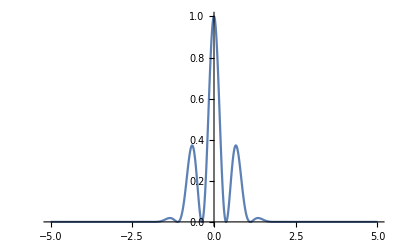

```mathematica
Plot[f[x]^2,{x,-5,5},PlotRange->All]
```

```mathematica
coef[j_]:=Evaluate[(1/(2 π))Integrate[f[x]^2 Exp[-I j x],{x,-π,π}]]
```

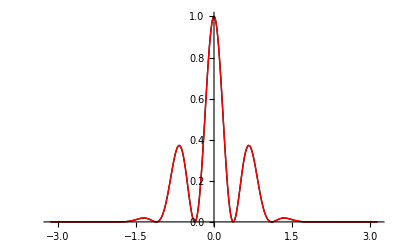

```mathematica
Plot[{f[x]^2,Re[Evaluate[Sum[coef[j] Exp[I j x],{j,-20,20}]]]},{x,-π,π},
PlotStyle->{{Black,Thick},{Red,Thick}},PlotRange->All]
```

```mathematica
NIntegrate[Abs[f[x]^2 - Evaluate[Sum[coef[j] Exp[I j x],{j,-20,20}]]]^2,{x,-π,π}]
```

3.75724×10^-19